```mathematica
normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}]
decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];];
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]

multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
jJ=0.5;
mJs=Range[-jJ,jJ,1];

mom =0.001/198;
ClearAll;
ImgSize=900;
workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/systems/mul_helion_miwchan_3/results";
SetDirectory[workingdirectory]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan_3/results

#### Read LHS ⟨ ϕ_(3He)^n|(Ĥ)_(V18+UIX)|ϕ_(3He)^m ⟩, m,n∈{1,N_He3}

```mathematica
HeNormHamMat=ReadList["./mat_npp0.5^+",Number];
HeBasisDim=HeNormHamMat[[1]];
HeNorm=ArrayReshape[HeNormHamMat[[2;;HeBasisDim^2+1]],{HeBasisDim,HeBasisDim}];HeHam=ArrayReshape[HeNormHamMat[[HeBasisDim^2+2;;2 HeBasisDim^2+1]],{HeBasisDim,HeBasisDim}];
groundstate=Sort[Transpose[Eigensystem[{HeHam,HeNorm}]]][[4]];
e0=groundstate[[1]];
Print["N_He3 = ",HeBasisDim,";   B_0(He) = ",e0," MeV"];
```

N_He3 = 490;   B_0(He) = -5.31212+0. ⅈ MeV

```mathematica
(HeHam.groundstate[[2]])[[;;4]]//MatrixForm
(groundstate[[1]] HeNorm.groundstate[[2]])[[;;4]]//MatrixForm
Norm[groundstate[[2]]]
```

(0.000104858+0. ⅈ
0.000116923+0. ⅈ
0.000093439+0. ⅈ
0.0000576173+0. ⅈ)

(0.000104858+0. ⅈ
0.000116923+0. ⅈ
0.000093439+0. ⅈ
0.0000576173+0. ⅈ)

1.

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
LitNormHamMat=ReadList["./mat_"<>ToString[jJ]<>"^"<>parity,Number];
LITbasisDim=LitNormHamMat[[1]];
LitNorm=ArrayReshape[LitNormHamMat[[2;;LITbasisDim^2+1]],{LITbasisDim,LITbasisDim}];LitHam=ArrayReshape[LitNormHamMat[[LITbasisDim^2+2;;2 LITbasisDim^2+1]],{LITbasisDim,LITbasisDim}];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = 3210

#### Read RHS ⟨ ϕ_(lit+He3)^n|O_Lm_L|ϕ_(lit+He3)^m ⟩, n,m∈{1,N_LIT/n_k+N_He3}

the calculation is parallel in n_k parts

```mathematica
nk=Max[ToExpression[StringSplit[FileNames["*_inhomo*"],"_"][[All,1]]]];
ks=Range[0,nk];
mJ=mJs[[1]];
mL=mLs[[1]];
If[Abs[mJ-mL]≤1/2,
files="./"<>ToString[#]<>"_inhomo1-1_J"<>ToString[jJ]<>"_mJ"<>ToString[mJ]<>"-mL"<>ToString[mL]<>".log"&/@ks,
files="./"<>ToString[#]<>"_inhomo1-1_J"<>ToString[jJ]<>"_mJ"<>ToString[mJ]<>"-mL"<>ToString[-mL]<>".log"&/@ks
]

inhomos=SparseArray[ReadList[#,Number,RecordLists->True]]&/@files;
CouplingMatrices=SparseArray[ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]]&/@inhomos;
```

{./0_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./1_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./2_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./3_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./4_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./5_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./6_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./7_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./8_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./9_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./10_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./11_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./12_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./13_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./14_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./15_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./16_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./17_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./18_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./19_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./20_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./21_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./22_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./23_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./24_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./25_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./26_inhomo1-1_J0.5_mJ-0.5-mL-1.log}

```mathematica
Dimensions[inhomos[[1]]]
Dimensions[CouplingMatrices[[1]]]
```

{372100,1}

{610,610}

#### Read expansion coefficients of He3 |He3 ⟩=∑_(m=1)^N_He3 c_m·|ϕ_He3^m ⟩

```mathematica
(*coeffs=RandomReal[{0,10^(-4)},HeBasisDim];*)
coeffs=Chop[groundstate[[2]],5^(-1)];
Print["N_He3 = ",Length[coeffs]," = ",HeBasisDim,"  ⟨0|0⟩ = ",Norm[coeffs]];
```

N_He3 = 490 = 490  ⟨0|0⟩ = 0.769232

#### calculate the components of the RHS inhomogeneity vector by summing up the ME’s of one row with each column weighted by the corresponding |He3 ⟩ coefficient

```mathematica
CouplingBloxx=#[[HeBasisDim+1;;,;;HeBasisDim]]&/@CouplingMatrices;
RHSComponents=#.coeffs&/@CouplingBloxx;
RHSVector=Flatten[RHSComponents];
If[Length[RHSVector]≠LITbasisDim,Print["LIT state dimension of RHS("<>ToString[Length[RHSVector]]<>") and LHS("<>ToString[LITbasisDim]<>") inconsistent!"]]
Dimensions[CouplingBloxx[[1]]]
```

{120,490}

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=5.;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];

threshold=10^(-25);

testfu=0;testcompo={};

inhomo=(2/mom) RHSVector;

Clear[litcomp];
litcomp[threshold_]:=Block[{λscf=Transpose[decompose[threshold,LitNorm,LitHam]]},Plus@@((Abs[#[[2]]]^2/((#[[1]]-e0-σRe)^2+σI^2))&/@λscf)];

testfu+=Evaluate[litcomp[threshold]];

tmps=Transpose[decompose[threshold]];

testcompo=AppendTo[testcompo,Re[tmps]];

LIT=(-1)^(jJ-0.5) testfu;
LITcompo=Flatten[testcompo,1];

LITcompo=Transpose[{LITcompo[[All,1]],Re[(-1)^(jJ-0.5) LITcompo[[All,2]]]}];

Plot[LIT,{σRe,-10,100},PlotRange->{Automatic,Full},MaxRecursion->0,PlotPoints->60,MeshFunctions->{#&},Mesh->120,MeshStyle->PointSize[Large],
PlotLabel->"EV basis N_ev > "<>ToString[N[threshold],TraditionalForm]<>"   σ_I = "<>ToString[σI],AxesLabel->{Style["σ_R [MeV]",Blue,18],Style["LIT [fm^3 × MeV^-1]",Blue,18]},ImageSize->ImgSize,PlotLegends->{"J="<>ToString[jJ]},ImageSize->ImgSize]

maxi=1.05 Max[Select[LITcompo,#[[1]]<100&][[All,2]]];
mini=0.95 Min[Select[LITcompo,#[[1]]<100&][[All,2]]];
strengthfunctionBare=Transpose[{LITcompo[[All,1]],(LITcompo[[All,2]]^2)}];
ListPlot[strengthfunctionBare,Joined->False,PlotRange->{{-10,120},{Automatic,Automatic}},AxesLabel->{Style["E [MeV]",Blue,18],Style["SubsuperscriptBox[F, ν' L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]",Blue,18]},PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[ks]]]]&[Floor[i-1,1]+1],{i,1,Length[ks]}],PlotLegends->{"I_n="<>ToString[jJ]},ImageSize->ImgSize]
```

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

Part::partw: Part 2 of Re[Transpose[decompose[1/10000000000000000000000000]]] does not exist.

Transpose::nmtx: The first two levels of {{Transpose[decompose[1/10000000000000000000000000]]},Re[(1.+0. ⅈ) {Re[Transpose[decompose[«1»]]]}⟦All,2⟧]} cannot be transposed.

-Graphics-

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of {Transpose[decompose[1/10000000000000000000000000]]} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[{Transpose[decompose[1/10000000000000000000000000]]}],Transpose[Re[(1.+0. ⅈ) {Re[«1»]}⟦All,2⟧]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[decompose[1.×10^-25]]} cannot be transposed.

Part::partw: Part 2 of Re[Transpose[decompose[1.×10^-25]]] does not exist.

Transpose::nmtx: The first two levels of {Transpose[{Transpose[decompose[1.×10^-25]]}],Transpose[Re[(1.+0. ⅈ) {Re[«1»]}⟦All,2⟧]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[decompose[1.×10^-25]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of Re[Transpose[decompose[1.×10^-25]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: Transpose[{Transpose[{Transpose[decompose[1.×10^-25]]}],Transpose[Re[(1.+0. ⅈ) {«1»}⟦All,2⟧]]^2}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Transpose[{Transpose[{Transpose[decompose[1/10000000000000000000000000]]}],Transpose[Re[(1.+0. ⅈ) {Re[Transpose[decompose[1/10000000000000000000000000]]]}⟦All,2⟧]]^2}],Joined→False,PlotRange→{{-10,120},{Automatic,Automatic}},AxesLabel→{E [MeV],SubsuperscriptBox[F, ν' L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]},PlotStyle→{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.3763885925925926, 0.11398911111111111, 0.6084696296296296],RGBColor[0.29988740740740744, 0.13754407407407407, 0.6838547407407407],RGBColor[0.2641351111111111, 0.20142911111111111, 0.745889111111111],RGBColor[0.24826577777777778, 0.275703037037037, 0.7865342222222222],RGBColor[0.24432622222222222, 0.3562102962962963, 0.8143457777777778],RGBColor[0.2563255555555556, 0.43092088888888885, 0.8085534444444444],RGBColor[0.27201785185185184, 0.5013174814814815, 0.793215962962963],RGBColor[0.29560125925925923, 0.5599314074074073, 0.7559638148148149],RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334],RGBColor[0.35643844444444445, 0.6505601851851851, 0.6526530370370371],RGBColor[0.39644548148148145, 0.6796575185185184, 0.5910551851851853],RGBColor[0.4391281111111111, 0.7049679999999999, 0.5292500000000001],RGBColor[0.488654037037037, 0.7216026666666666, 0.4702046666666667],RGBColor[0.5413381851851852, 0.7340082962962963, 0.4163578518518519],RGBColor[0.5971805555555556, 0.7421848888888889, 0.3677095555555555],RGBColor[0.654541037037037, 0.7431753703703704, 0.32997788888888896],RGBColor[0.7116684444444445, 0.7410033703703703, 0.29632714814814815],RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.8124282962962963, 0.7080947037037036, 0.254538074074074],RGBColor[0.8532952592592592, 0.6782357407407408, 0.24015881481481482],RGBColor[0.8801795555555555, 0.6316843333333333, 0.22766533333333333],RGBColor[0.9010821111111111, 0.5780533333333334, 0.21563355555555558],RGBColor[0.9021718888888889, 0.5016906666666666, 0.20109844444444444],RGBColor[0.8973538888888889, 0.4182404444444446, 0.18500666666666668],RGBColor[0.8826895925925926, 0.3229776296296296, 0.16632044444444444],RGBColor[0.8696541111111111, 0.22716644444444462, 0.1489297777777778]},PlotLegends→{I_n=0.5},ImageSize→900]

{3210}

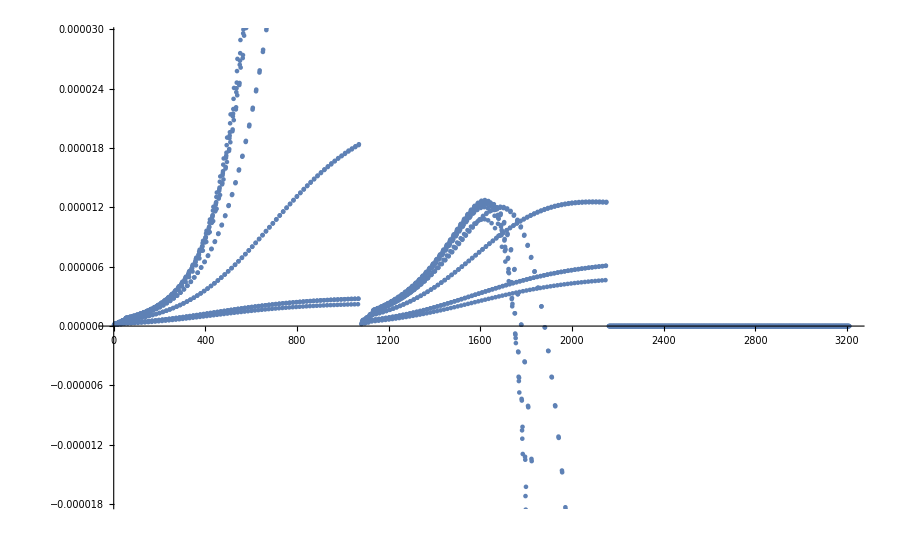

```mathematica
Dimensions[RHSVector]
ListPlot[RHSVector,ImageSize->ImgSize]
```

```mathematica
(*ListPlot3D[CouplingBloxx,ImageSize->ImgSize]*)
```